```mathematica
ClearAll[files,importfile,raw]
files=FileNames["*.xlsx",NotebookDirectory[]]
{"/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/351/Книга3.xlsx","/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/351/~$Книга3.xlsx"}
importfile=files⟦1⟧
"/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/351/Книга3.xlsx"
raw = Import[importfile];
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

{/Users/leonidbarinov/Desktop/latexlabs/6 семестр/11.3/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/6 семестр/11.3/~$Книга1.xlsx}

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/351/Книга3.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/351/~$Книга3.xlsx}

/Users/leonidbarinov/Desktop/latexlabs/6 семестр/11.3/Книга1.xlsx

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/351/Книга3.xlsx

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

## Dataset1

```mathematica
dataset1= makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"a"->(Around[#a, #da] &),"lnr"-> (Around[#lnr, #dlnr] &)|>]
```

Dataset[<>]

```mathematica
line1 =LinearModelFit[(Normal@dataset1[All,{"a","lnr"}/*Values]),{1,x},x]
```

FittedModel[-15.9341+6.40512 x]

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -15.9341 | 0.706998 | -22.5378 | 8.37202×10^-12
x | 6.40512 | 0.225432 | 28.4126 | 4.36031×10^-13

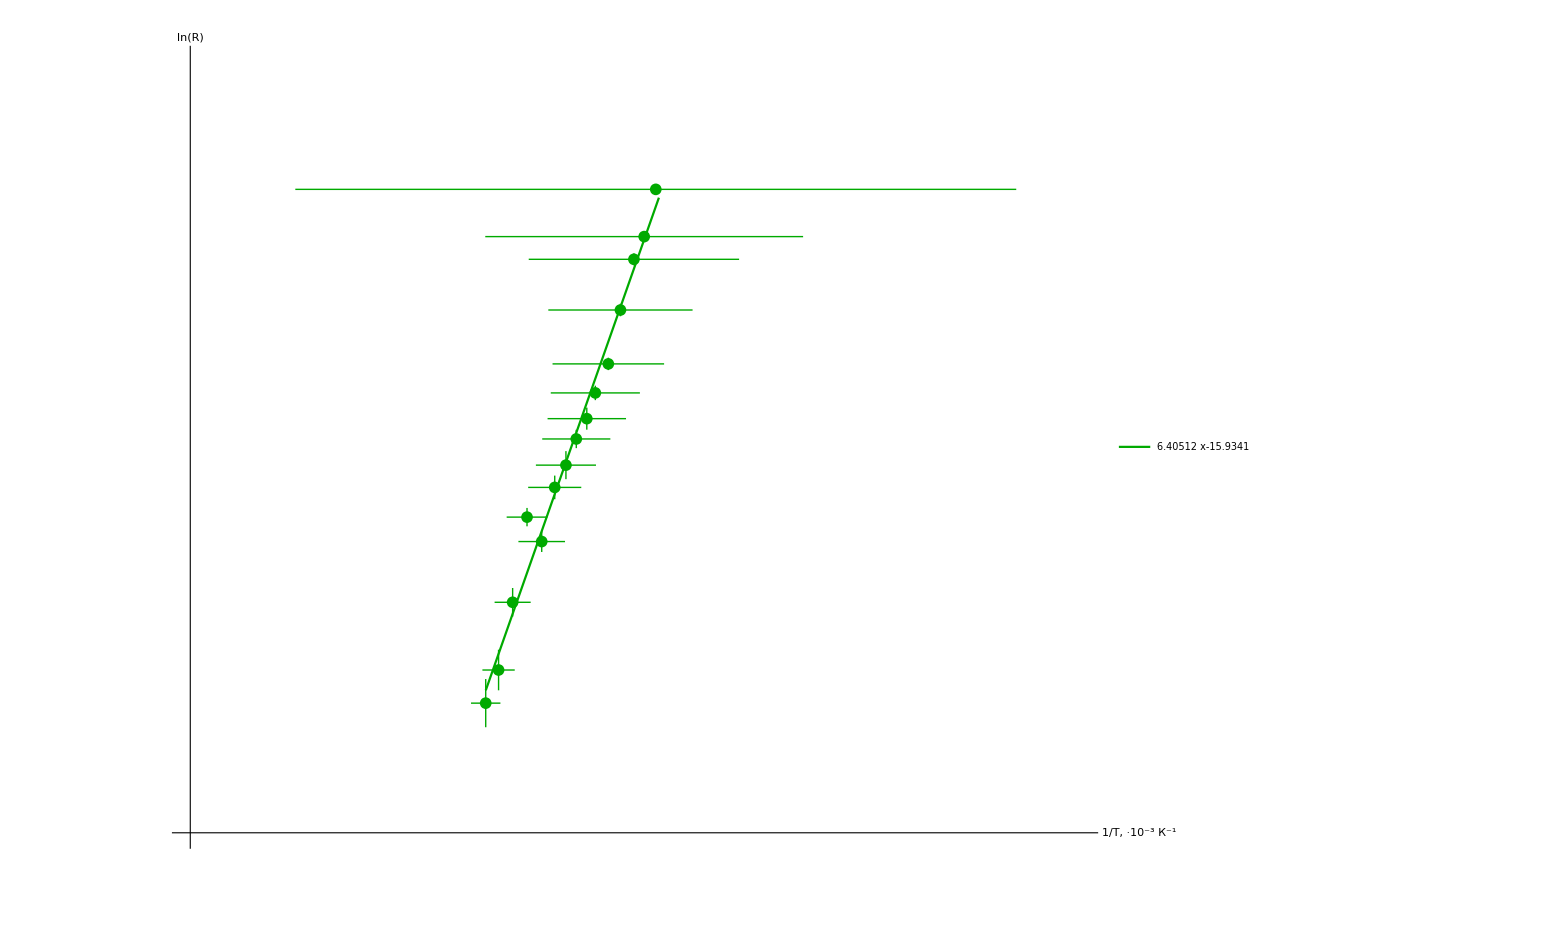

```mathematica
Show[
ListPlot[
{dataset1WithErrs},
PlotRange-> {{2.25,4.3},{2.1,6.1}},
Ticks-> {Range[-1000,1000, 0.25],Range[-1000,1000, 0.5]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["1/T, ·10^-3 (:041a)^-1", Large], Style["ln(R)", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 0.05],Range[-1000,1000, 0.1]},
LabelStyle->Black,
PlotStyle->Darker@Green
(*Joined->True,
InterpolationOrder->3,*)
(*PlotLegends->Placed[LineLegend[
{Normal@line3},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.3],Scaled[0.75]}
]*)
],
Plot[{line1[x]},{x,2.931,3.33},
PlotLegends->Placed[LineLegend[
{Normal@line1},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.2],Scaled[0.6]}
],
PlotStyle->Darker@Green
]
]
```

```mathematica
MaTeX["1/T,\: \\textrm{K}^{-1}"]
```

-Graphics-